```mathematica
ex1[k_]:=1-2ex1[k-1]^2
ex1[0]=0.86;
Table[ex1[k],{k,1,5}]
```

{-0.4792,0.540735,0.415212,0.655198,0.141431}

```mathematica
ex2[k_]:=4 ex2[k-1]-2 ex2[k-1]^2
ex2[0]=0.2;
Table[ex2[k],{k,1,6}]
```

{0.72,1.8432,0.578028,1.64388,1.17084,1.94163}

```mathematica
ex3[k_]:=ex3[k-1]-ex3[k-2]
ex3[0]=1;
ex3[1]=2;
Table[ex3[k],{k,1,8}]
```

{2,1,-1,-2,-1,1,2,1}

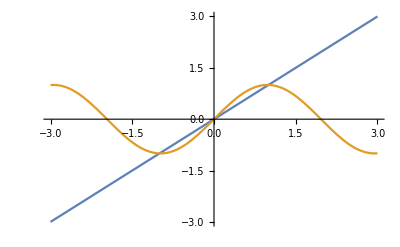

{x→-0.999592}

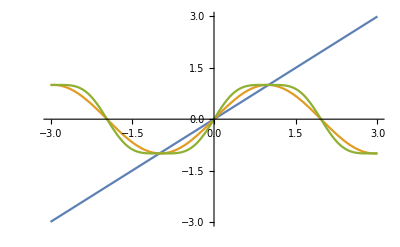

```mathematica
f05[x_]=Sin[1.6x];
Plot[{x,f05[x]},{x,-3,3}]
FindRoot[f05[x]==x,{x,-1}]
Plot[{x,f05[x],f05[f05[x]]},{x,-3,3}]
```

{0.95,0.2375,0.389352,0.655592,0.863057,0.549846,0.8414,0.609262,0.865842,0.541694,0.835842,0.623397,0.867155,0.537811,0.83302,0.630403,0.867117,0.537924,0.833104,0.630196,0.867125}

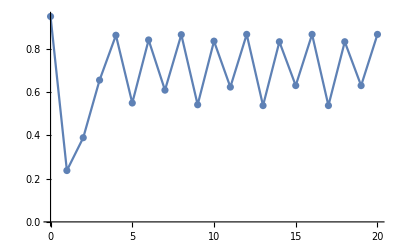

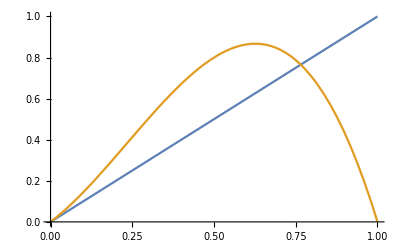

{{x→-0.0653312},{x→0.},{x→0.765331}}

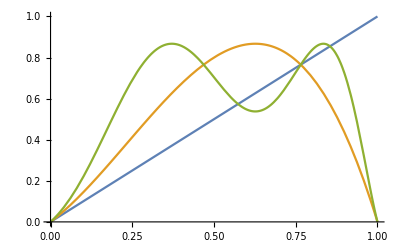

{{x→-0.591325},{x→-0.266767-0.192267 ⅈ},{x→-0.266767+0.192267 ⅈ},{x→-0.0653312},{x→0.},{x→0.573635},{x→0.765331},{x→0.854687},{x→1.09654}}

```mathematica
f06[x_]=1.2x+2.8x^2-4x^3;
NestList[f06,0.95,20]
ListPlot[NestList[f06,0.95,20],DataRange->{0,20},Joined->True, Mesh->All]
Plot[{x,f06[x]},{x,0,1}]
Solve[f06[x]==x]
Plot[{x,f06[x],f06[f06[x]]},{x,0,1}]
Solve[f06[f06[x]]==x]
```

-1.82-0.74 x-0.16 x^2

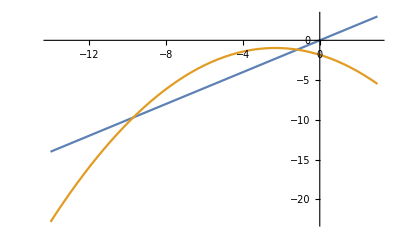

{{x→-9.70264},{x→-1.17236}}

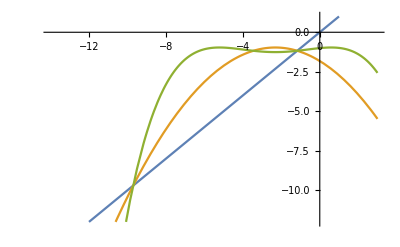

{{x→-9.70264},{x→-1.17236},{x→0.8125-4.56849 ⅈ},{x→0.8125+4.56849 ⅈ}}

```mathematica
f07[x_]=-1.82-0.74x-0.16x^2
Plot[{x,f07[x]},{x,-14,3}]
Solve[f07[x]==x]
Plot[{x,f07[x],f07[f07[x]]},{x,-14,3},PlotRange->{-12,1}]
Solve[f07[f07[x]]==x]
```

1.982-2.306 x-0.708 x^2

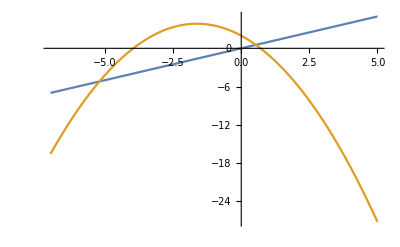

{{x→-5.20711},{x→0.537618}}

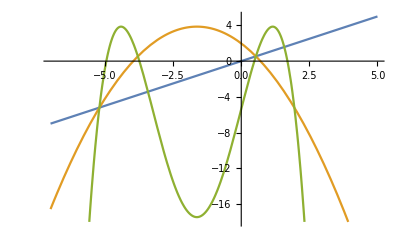

{{x→-5.20711},{x→-3.42342},{x→0.537618},{x→1.57879}}

```mathematica
f08[x_]=1.982-2.306x-0.708x^2
Plot[{x,f08[x]},{x,-7,5}]
Solve[f08[x]==x]
Plot[{x,f08[x],f08[f08[x]]},{x,-7,5}, PlotRange->{-18,5}]
Solve[f08[f08[x]]==x]
```

-1.284-3.128 x-2.671 x^2-0.722 x^3

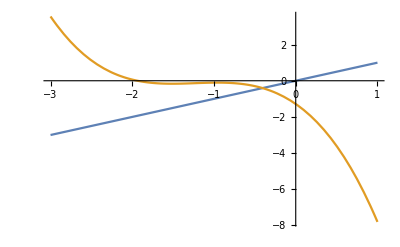

{{x→-1.64673-1.29175 ⅈ},{x→-1.64673+1.29175 ⅈ},{x→-0.405996}}

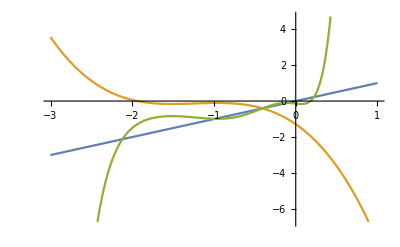

{{x→-2.20553-1.10543 ⅈ},{x→-2.20553+1.10543 ⅈ},{x→-2.12026},{x→-1.64673-1.29175 ⅈ},{x→-1.64673+1.29175 ⅈ},{x→-0.98568},{x→-0.405996},{x→-0.104418},{x→0.222521}}

-0.104418

{-2.20553-1.10543 ⅈ,-2.20553+1.10543 ⅈ,-2.12026,-1.64673-1.29175 ⅈ,-1.64673+1.29175 ⅈ,-0.98568,-0.405996,-0.104418,0.222521}

0.222521

-0.104418

-0.98568

-2.12026

```mathematica
f09[x_]=-1.284-3.128x-2.671x^2-0.722x^3
Plot[{x,f09[x]},{x,-3,1}]
Solve[f09[x]==x]
Plot[{x,f09[x],f09[f09[x]]},{x,-3,1}]
Solve[f09[f09[x]]==x]
f09[-0.9856799271135451]
solucoes08=x/.Solve[f09[f09[x]]==x]
f09[Part[solucoes08,3]]
f09[Part[solucoes08,6]]
f09[Part[solucoes08,8]]
f09[Part[solucoes08,9]]
```